Define everything in one place.

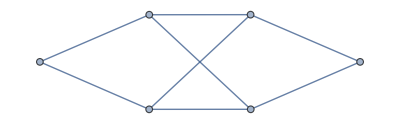

```mathematica
SetDirectory["~/Documents/UNH/Research/code/OTimes/sp4/"];
Clear[GammaAdj, GammaSymb, q, rho,n, dim, lvl, braid];
GammaAdj = { 
{0,1,1,0,0,0},
{1,0,0,1,1,0},
{1,0,0,1,1,0}, 
{0,1,1,0,0,1},
{0,1,1,0,0,1},
{0,0,0,1,1,0} 
};
AdjacencyGraph[ GammaAdj] (* picture of the graph *)
Clear[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo, pp];
SetNonCommutative[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo, pp];
GammaSymb = { 
{0,aa,bb,0,0,0},
{cc,0,0,dd,ee,0},
{ff,0,0,gg,hh,0}, 
{0,ii,jj,0,0,kk},
{0,ll,mm,0,0,nn},
{0,0,0,oo,pp,0}
};
quan[n_, qew_]:=(qew^n-qew^-n)/(qew-qew^-1);
inDeg[z_]:=360(z//Arg)/(2Pi)//N
dim=2;
lvl = 3;
q=Exp[(2Pi I)/(4(dim+lvl+1))];
rho = q^5; (* should this be -q^5??? *)

Hom0to2 = GetHomBasisList[GammaSymb, 0,2];
Hom0to0 = GetHomBasisList[GammaSymb,0,0];
Hom1to1 = GetHomBasisList[GammaSymb,1,1];
Hom2to4 = GetHomBasisList[GammaSymb, 2,4];
Hom2to3 = GetHomBasisList[GammaSymb, 2,3];
Hom2to2 = GetHomBasisList[GammaSymb,2,2];
Hom2to1 = GetHomBasisList[GammaSymb,2,1];
Hom2to0 = GetHomBasisList[GammaSymb,2,0];
Hom1to2 = GetHomBasisList[GammaSymb,1,2];
Hom1to1 = GetHomBasisList[GammaSymb,1,1];
Hom1to0 = GetHomBasisList[GammaSymb,1,0];
Hom0to1 = GetHomBasisList[GammaSymb,0,1];
Hom0to0 = GetHomBasisList[GammaSymb,0,0];
Hom0to2 = GetHomBasisList[GammaSymb, 0,2];
Hom3to3 = GetHomBasisList[GammaSymb, 3,3];
Cap = GenerateCap[GammaAdj, GammaSymb];
Cup = InTermsOf[Dagger[Cap], Hom0to2];
Cup = ScaleByConstant[Cup, -1];
Stick = GenerateStick[GammaAdj, GammaSymb];
DoubleStick = InTermsOf[BigTens[Stick, Stick], Hom2to2];

braidSol = {Root"-0.354"+"0.612" ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738,Root"0.612"+"0.354" ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945,Root"0.612"+"0.354" ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945,Root"-0.354"+"0.612" ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738,Root"0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,8]0.6580370064762462,1/2,1,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,1/4 ⅈ (-√2+2 ⅈ 3^(1/4)+√6),1/4 (-1+√3),1+√3,Root"0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,8]0.6580370064762462,(-1)^(5/12)+Root"-0.518" ⅈRoot[1+4 #1^2+#1^4&,3]0.,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"-0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257,Root"-0.448"+"0.259" ⅈRoot[1-4 #1^2+15 #1^4-4 #1^6+#1^8&,4]-0.4482877360840268,-√(-1+√3),-√(2 (1+√3)),-1/2 √(-1+√3),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,√(2+√3),Root"-0.157"Root[-1+40 #1^2+32 #1^4&,1]-0.15658560865650772,(√(2-√3))/2,Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,-1/(√2),-1/(√2),1/2 (3^(1/4)+Root"0.518" ⅈRoot[1+4 #1^2+#1^4&,4]0.),((1/2+ⅈ/2) ((-2+ⅈ)+√3))/(√2),-1/2 √(-1+√3),Root"-0.157"Root[-1+40 #1^2+32 #1^4&,1]-0.15658560865650772,-√(-1+√3),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,(√(2-√3))/2,-√(2 (1+√3)),√(2+√3),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,(-1)^(5/12)+Root"-0.518" ⅈRoot[1+4 #1^2+#1^4&,3]0.,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257,Root"0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,8]0.6580370064762462,(√(2-√3))/2,√(2+√3),1/4 ⅈ (-√2+2 ⅈ 3^(1/4)+√6),1/2 (3^(1/4)+Root"0.518" ⅈRoot[1+4 #1^2+#1^4&,4]0.),1,1/2,1/4 ⅈ (-√2+2 ⅈ 3^(1/4)+√6),Root"-0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,(-1)^(5/12)+Root"-0.518" ⅈRoot[1+4 #1^2+#1^4&,3]0.,Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,1/4 (√2-√6),√(1/2 (-1+√3)),-√(2+√3),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,-√(1+√3),√(1/2 (-1+√3)),-1/2 √(-5+3 √3),Root"-0.448"+"0.259" ⅈRoot[1-4 #1^2+15 #1^4-4 #1^6+#1^8&,4]-0.4482877360840268,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,1+√3,1/4 (-1+√3),1/2 (3^(1/4)+Root"0.518" ⅈRoot[1+4 #1^2+#1^4&,4]0.),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,-√(2+√3),√(1/2 (-1+√3)),1/4 (√2-√6),Root"-0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,4]-0.25881904510252074,-1/2 √(-5+3 √3),√(1/2 (-1+√3)),-√(1+√3),(ⅈ-√3)/(√2+√6),Root"0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,8]0.48171652200114257,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.259"+"0.259" ⅈRoot[1+56 #1^4+16 #1^8&,6]0.25881904510252074,Root"-0.482"+"0.518" ⅈRoot[1+56 #1^2+24 #1^4+224 #1^6+16 #1^8&,2]-0.48171652200114257,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,Root"-0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,6]-0.5630162503052472,Root"0.563"+"0.221" ⅈRoot[1-8 #1^2+24 #1^4-32 #1^6+4 #1^8&,8]0.5630162503052472,(-1)^(5/12)+Root"-0.518" ⅈRoot[1+4 #1^2+#1^4&,3]0.,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,-1/(√2),-1/(√2),Root"0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,8]0.6580370064762462,1/2 (3^(1/4)+Root"0.518" ⅈRoot[1+4 #1^2+#1^4&,4]0.),√(2+√3),(√(2-√3))/2,Root"-0.658"+"0.259" ⅈRoot[1+8 #1^2-24 #1^4+32 #1^6+16 #1^8&,2]-0.6580370064762462,Root"-0.354"+"0.612" ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738,Root"0.612"+"0.354" ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945,Root"0.612"+"0.354" ⅈRoot[1-2 #1^2+4 #1^4&,4]0.6123724356957945,Root"-0.354"+"0.612" ⅈRoot[1+2 #1^2+4 #1^4&,2]-0.3535533905932738};
braid = Hom2to2;
For[i=1,i<=Length[Hom2to2],i++,
braid[[i]][["scalar"]] = braidSol[[i]]
];
braid = braid//GPARootReduce;
```